```mathematica
Isc= 30*100^2/10002
```

```mathematica
300
Isc1= 30
```

300

30

```mathematica
kb= 1.3*10^(-19)
T=294
V1=0.6
e=1.6*10^(-19)
```

1.3×10^-19

294

0.6

1.6×10^-19

```mathematica
I0=Isc1/(Exp[(V1*e)/(kb*T)])
```

29.9247

```mathematica
(kb*T)/e*Log[Isc1*100/(I0)]
```

```mathematica
1100.6600281779051
"open circuit"
Exp[e*0.7/(kb*T)]
```

1100.66

open circuit

1.00293

```mathematica
Exp[e*0.7/(kb*T)]
```

1.00293

```mathematica
ϕp=(q*Na/(ϵ))*(x^2/2+x*xp)
```

(Na q (x^2/2+√2 x √((Nd ϵ)/(Na (Na+Nd) q))))/ϵ

```mathematica
ϕn=(-q*Nd/(ϵ))*(x^2/2-x*xn)
```

-(Nd q (x^2/2-√2 x √((Na ϵ)/(Nd (Na+Nd) q))))/ϵ

```mathematica
ϕn-ϕp
```

-(Nd q (x^2/2+x xn))/(ϵ ϵ0)-(Na q (x^2/2+x xp))/(ϵ ϵ0)

```mathematica
Simplify[-(Nd q (x^2/2+x xn))/(ϵ ϵ0)-(Na q (x^2/2+x xp))/(ϵ ϵ0)]
```

-(q x (Nd (x+2 xn)+Na (x+2 xp)))/(2 ϵ ϵ0)

```mathematica
f[x_]=(q*Na/(ϵ*ϵ0))*(x^2/2+x*xp1)
```

(Na q (x^2/2+x xp1))/(ϵ ϵ0)

```mathematica
g[x_]=(-q*Nd/(ϵ*ϵ0))*(x^2/2-x*xn1)
```

-(Nd q (x^2/2-x xn1))/(ϵ ϵ0)

```mathematica
Abs[f[-xp1]]
```

1/2 Abs[(Na q xp1^2)/(ϵ ϵ0)]

```mathematica
Solve[3/2 Abs[(Na q xp1^2)/(ϵ ϵ0)],xp1]
```

Solve::naqs: 3/2 Abs[(Na q xp1^2)/(ϵ ϵ0)] is not a quantified system of equations and inequalities.

```mathematica
Solve[U==3/2 Abs[(Na q xp1^2)/(ϵ ϵ0)],xp1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xp1→-(√(2/3) √U √ϵ √ϵ0)/(√Na √q)},{xp1→-(ⅈ √(2/3) √U √ϵ √ϵ0)/(√Na √q)},{xp1→(ⅈ √(2/3) √U √ϵ √ϵ0)/(√Na √q)},{xp1→(√(2/3) √U √ϵ √ϵ0)/(√Na √q)}}

```mathematica
Abs[g[xn1]]
```

1/2 Abs[(Nd q xn1^2)/(ϵ ϵ0)]

```mathematica
Solve[0==1/2 Abs[(Nd *q* xn1^2)/(ϵ *ϵ0)],{xn1}]
```

{{xn1→0}}

```mathematica
Ud= Abs[f[-xp1]]-Abs[g[xn1]]
```

-1/2 Abs[(Nd q xn1^2)/(ϵ ϵ0)]+1/2 Abs[(Na q xp1^2)/(ϵ ϵ0)]

```mathematica
NRoots[-1/2 (Nd q x^2)/(ϵ ϵ0)+3/2 (Na q xp1^2)/(ϵ ϵ0)==U,{x}]
```

General::ivar: {x} is not a valid variable.

NRoots[-(Nd q x^2)/(2 ϵ ϵ0)+(3 Na q xp1^2)/(2 ϵ ϵ0)==U,{x}]

```mathematica
f[xpi]
```

(Na q (xp1 xpi+xpi^2/2))/(ϵ ϵ0)

```mathematica
So]
```

```mathematica
Abs[f[]]
```

Abs[(Na q ((Na ϵ)/(Nd (Na+Nd) q)+2 √((Na ϵ)/(Nd (Na+Nd) q)) √((Nd ϵ)/(Na (Na+Nd) q))))/(ϵ ϵ0)]

```mathematica
f
```

f

```mathematica
f[xp1]
```

(3 Na q xp1^2)/(2 ϵ ϵ0)

WolframAlphaQueryResults

{ComplexInfinity==U,π x}

```mathematica
Solve[(3 Na q x^2)/(2 ϵ ϵo)==u,x]
```

{{x→-(√(2/3) √u √ϵ √ϵo)/(√Na √q)},{x→(√(2/3) √u √ϵ √ϵo)/(√Na √q)}}

```mathematica
g[xn1]
```

(Nd q xn1^2)/(2 ϵ ϵ0)

```mathematica
Solve[(Nd q x^2)/(2 ϵ)==u,x]
```

{{x→-(√2 √u √ϵ)/(√Nd √q)},{x→(√2 √u √ϵ)/(√Nd √q)}}

```mathematica
(√(2/3) √u √ϵ)/(√Na √q)+(√2 √u √ϵ)/(√Nd √q)
```

(√(2/3) √u √ϵ)/(√Na √q)+(√2 √u √ϵ)/(√Nd √q)

```mathematica
[(√2 √u √ϵ)/(√Na √q)+(√2 √u √ϵ)/(√Nd √q)]
```

```mathematica
-1/2 (Nd q xn1^2)/(ϵ ϵ0)+1/2 (Na q xp1^2)/(ϵ ϵ0)
```

-(Nd q xn1^2)/(2 ϵ ϵ0)+(Na q xp1^2)/(2 ϵ ϵ0)

```mathematica
Solve[-(Nd q xn1^2)/(2 ϵ ϵo)+(Na q xp1^2)/(2 ϵ ϵo)==U,xp1]
```

{{xp1→-(√(Nd q xn1^2+2 U ϵ ϵo))/(√Na √q)},{xp1→(√(Nd q xn1^2+2 U ϵ ϵo))/(√Na √q)}}

```mathematica
Solve[-(Nd q xn1^2)/(2 ϵ ϵo)+(Na q xp1^2)/(2 ϵ ϵo)==U,xn1]
```

{{xn1→-(√(Na q xp1^2-2 U ϵ ϵo))/(√Nd √q)},{xn1→(√(Na q xp1^2-2 U ϵ ϵo))/(√Nd √q)}}

```mathematica
(√(Na q xp1^2-2 U ϵ ϵo))/(√Nd √q)+(√(Nd q xn1^2+2 U ϵ ϵo))/(√Na √q)
```

(√(Na q xp1^2-2 U ϵ ϵo))/(√Nd √q)+(√(Nd q xn1^2+2 U ϵ ϵo))/(√Na √q)

```mathematica
FullSimplify[(√(Na q xp1^2-2 U ϵ ϵo))/(√Nd √q)+(√(Nd q xn1^2+2 U ϵ ϵo))/(√Na √q)]
```

((√(Na q xp1^2-2 U ϵ ϵo))/(√Nd)+(√(Nd q xn1^2+2 U ϵ ϵo))/(√Na))/(√q)

```mathematica
"Blatt 5"
Solve[Iv==Exp[(q*v)/(k*t)-1]-Isc,v]
```

Blatt 5

{{v→ConditionalExpression[-(k t (-1+2 ⅈ π C[1]+Log[1/(Isc+Iv)]))/q, C[1]∈ℤ]}}

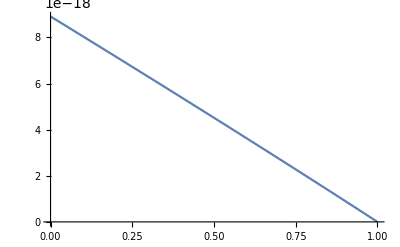

```mathematica
Plot[y=-36*((Log[(3*(1-b)+3)/2.5*10^(-10)]+1)*1.3*10^(-23)*300/1.6^10^(-19))*3*(1-b),{b,0,1}]
```

```mathematica
Edye= 2.16*10^(-19)
```

2.16×10^-19

```mathematica
h= 6.626*10^(-34)
```

6.626×10^-34

```mathematica
c= 299792458
```

299792458

```mathematica
h*c/Edye
```

9.19641×10^-7

```mathematica
9.196411234759262*^-7*10^9
```

919.641

```mathematica
50/1.5
```

33.3333

```mathematica
"Blatt 6"
P[A_]= 1/2*ρ*A*v^3
```

Blatt 6

1/2 A v^3 ρ

```mathematica
1.25*8^3/(2*10^6*Pi)
```

0.000101859

```mathematica
0.00010185916357881301*2
```

0.000203718

```mathematica
0.00020371832715762603*16/27*0.8
```

0.0000965776

```mathematica
Solve[10^6==1/2*1.25*8^3*x*16/27*0.8,x]
```

{{x→6591.8}}

```mathematica
6591.796875/Pi
```

2098.23

```mathematica
Sqrt[2098.2341130279174]
```

```mathematica
45.806485490898744*2
```

91.613

```mathematica
Solve[P==1/2*(a*ρ*v^3),a]
```

{{a→(2 P)/(v^3 ρ)}}

```mathematica
"ex3"
Cp[a_]=(1+a)/2*(1-a^2)mD=2.014u;mT=3.016u;mHe=4.0027u
```

ex3

1/2 (1+a) (1-a^2)

```mathematica
1/2 (1+a) (1-a^2)
```

1/2 (1+a) (1-a^2)

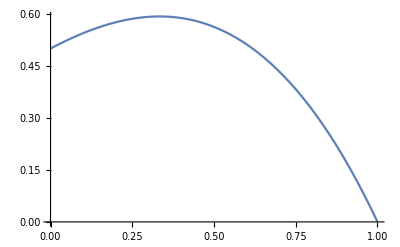

```mathematica
Plot[Cp[a],{a,0,1}]
```

```mathematica
D[Cp[a],a]
```

-a (1+a)+1/2 (1-a^2)

```mathematica
Simplify[-a (1+a)+1/2 (1-a^2)]
```

1/2 (1-2 a-3 a^2)

```mathematica
"Blatt8"
"ex3"
6.5*10^(-19)
```

Blatt8

ex3

6.5×10^-19

```mathematica
20000*3.6*10^6/(6.5*10^(-19))
```

1.10769×10^29

```mathematica
1.1076923076923077*^29 /(6.023*10^23)
```

183910.

```mathematica
183910* 12.01
```

2.20876×10^6

```mathematica
1/(2.20876*10^3)
```

0.000452743

```mathematica
-1.0087-139.91+235.04-93.91
```

0.2113

```mathematica
0.21129999999999427*1.6*10^(-27)
```

3.3808×10^-28

```mathematica
3.3807999999999085`10^-28
```

```mathematica
"3"

+2.014+ 3.016- 4.0027-1.0087
```

3

0.0186

```mathematica
2.014+ 3.016
```

5.03

```mathematica
1/(8.352510*10^(-27))
```

1.19724×10^26

```mathematica
3.08860239306×10^(-29)
```

3.0886×10^-29

```mathematica
3.08860239306*10^(-29)*C^2
```

```mathematica
3.08860239306*^-29 (3*10^8)^2
```

2.77974×10^-12

```mathematica
C
```

C

```mathematica
Information[C]
```

```mathematica
3.08860239306*^-29 (3*10^8)^2*1.197244900036037*^26
```

3.32803×10^14

```mathematica
3.3280321169971656*^14/(3.6*10^6*20000)
```

4622.27

```mathematica
1.5^2+3^2
```

11.25

```mathematica
Sqrt[11.5]
```

3.39116

```mathematica
1.25*10^-6/(2*Pi)*(40000/1.5003)
```

0.0053041

```mathematica
(2*(2.347418039703471*10^-3))*Cos[88.25]
```

0.00450492

```mathematica
"Shet9 Ex 2"
1000000*9.81*100
```

Shet9 Ex 2

9.81×10^8

```mathematica
12*60*60
```

43200

```mathematica
9.81*10 ^8 /(43200)
```

22708.3

```mathematica
"shet 9 A4"

Pi*2(0.5^2 -0,8^2)
```

shet 9 A4

```mathematica
Pi*2(-0.5^2 +0.8^2)
```

2.45044

```mathematica
2.4504422698000394*1600
```

3920.71

```mathematica
3920.707631680063*1/2 *(0.5^2+0.8^2)
```

1744.71

```mathematica
2*Pi/(1/10000)
```

20000 π

```mathematica
1/2*1744.7148960976283*(20000 π)^2
```

3.44393×10^12

```mathematica
0.005304103948940058*Cos[88.28]
```

0.00504246

```mathematica
f4cccccccc
```